```mathematica
(*STSGraph[n_]/;Mod[n,6]==1||Mod[n,6]==3:=STSGraph[n]=Import["sts/sts-"<>ToString[n]]*)
```

```mathematica
BoseGraph[n_]/;Mod[n,6]==3:=With[{k=(n-3)/6},Graph[TwoWayRule@@@Select[Subsets[Join[Flatten[Table[{{x,i},{y,i},{Mod[(k+1)(x+y),2k+1],Mod[i+1,3]}},{x,0,2k},{y,x+1,2k},{i,0,2}],2],Table[{{x,0},{x,1},{x,2}},{x,0,2k}]],{2}],!DisjointQ@@#&]]]
```

```mathematica
SkolemGraph[n_]/;Mod[n,6]==1:=With[{k=(n-1)/6},Graph[TwoWayRule@@@Select[Subsets[Join[
Flatten[Table[{{x,i},{y,i},{Floor[Mod[x+y,2k]/2]+If[Mod[x+y,2]==1,k,0],Mod[i+1,3]}},{i,0,2},{x,0,2k-1},{y,x+1,2k-1}],2],
Flatten[Table[{Infinity,{k+x,i},{x,Mod[i+1,3]}},{x,0,k-1},{i,0,2}],1],
Table[{{x,0},{x,1},{x,2}},{x,0,k-1}]
],{2}],!DisjointQ@@#&]]]
```

```mathematica
STSGraph[n_]/;Mod[n,6]==1||Mod[n,6]==3:=STSGraph[n]=If[Mod[n,6]==1,SkolemGraph[n],BoseGraph[n]]
```

```mathematica
StronglyRegularGraphQ[G_Graph,v_,k_,l_,u_]:=Block[{A,B},
A=AdjacencyMatrix[G];
B=A.A;
And[
VertexCount[G]==v,
MissingQ@SelectFirst[VertexDegree[G],#≠k&],
B*A==l*A,
B*(1-A-IdentityMatrix[v])==u*(1-A-IdentityMatrix[v])
]]
```

Testing

```mathematica
(*Table[IsomorphicGraphQ[BoseGraph[v],STSGraph[v]],{v,9,60,6}]*)
```

{True,True,True,True,True,True,True,True,True}

```mathematica
Table[StronglyRegularGraphQ[BoseGraph[v],v(v-1)/6,3(v-3)/2,(v+3)/2,9],{v,9,60,6}]
```

{True,True,True,True,True,True,True,True,True}

```mathematica
(*Table[IsomorphicGraphQ[SkolemGraph[v],STSGraph[v]],{v,7,60,6}]*)
```

{True,True,True,True,True,True,True,True,True}

```mathematica
Table[StronglyRegularGraphQ[SkolemGraph[v],v(v-1)/6,3(v-3)/2,(v+3)/2,9],{v,7,60,6}]
```

{True,True,True,True,True,True,True,True,True}

Blocks for a STS(9).

```mathematica
STSGraph[9]//VertexList
```

{{{0,0},{1,0},{2,1}},{{0,0},{2,0},{1,1}},{{0,1},{2,1},{1,2}},{{0,2},{2,2},{1,0}},{{1,0},{2,0},{0,1}},{{1,1},{2,1},{0,2}},{{1,2},{2,2},{0,0}},{{0,0},{0,1},{0,2}},{{1,0},{1,1},{1,2}},{{2,0},{2,1},{2,2}},{{0,1},{1,1},{2,2}},{{0,2},{1,2},{2,0}}}

Maximum Independent Set.

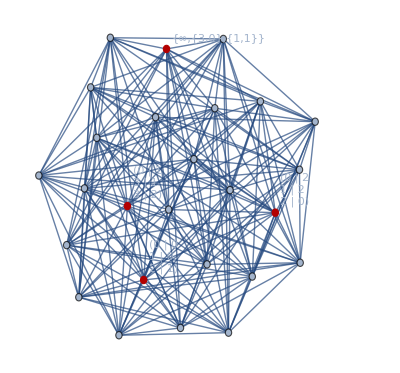

```mathematica
HighlightGraph[STSGraph[13],FindIndependentVertexSet@STSGraph[13],VertexLabels->Automatic]
```

```mathematica
Table[First@FindIndependentVertexSet@STSGraph[v],{v,7,31,6}]
```

{{{{0,0},{1,0},{1,1}}},{{{0,0},{1,0},{2,1}},{{0,2},{1,2},{2,0}},{∞,{3,0},{1,1}},{{0,1},{3,1},{3,2}}},{{{2,1},{3,1},{5,2}},{{0,0},{0,1},{0,2}},{{1,0},{1,1},{1,2}},{{4,0},{5,0},{4,1}},{{3,2},{4,2},{3,0}},{∞,{5,1},{2,2}}},{{{4,1},{5,1},{4,2}},{{1,0},{1,1},{1,2}},{{2,0},{4,0},{3,1}},{{3,0},{5,0},{0,1}},{{2,1},{6,1},{0,2}},{{6,2},{7,2},{6,0}},{{2,2},{5,2},{7,0}},{∞,{7,1},{3,2}}},{{{0,0},{4,0},{2,1}},{{5,1},{6,1},{5,2}},{{2,0},{6,0},{4,1}},{{1,1},{3,1},{2,2}},{{3,0},{7,0},{0,1}},{{7,1},{8,1},{7,2}},{{0,2},{1,2},{5,0}},{{8,2},{9,2},{8,0}},{{3,2},{6,2},{9,0}},{∞,{9,1},{4,2}}}}

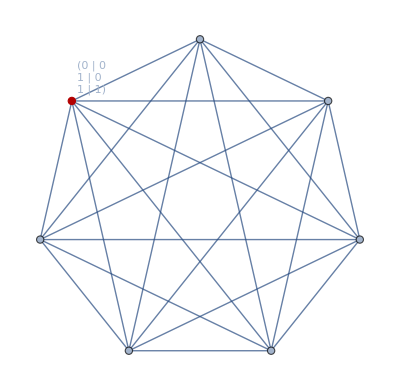
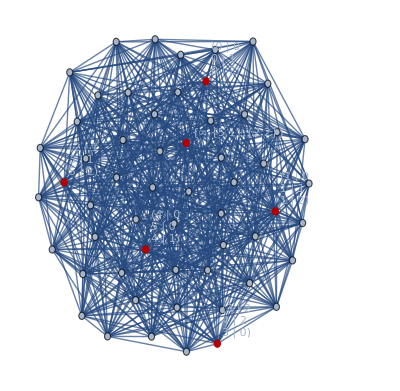
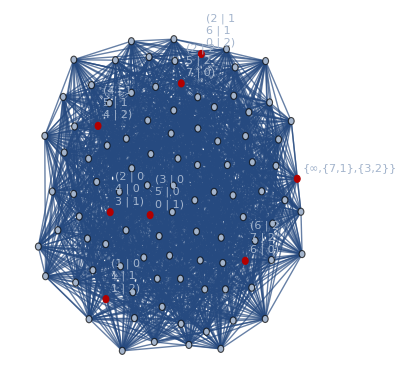
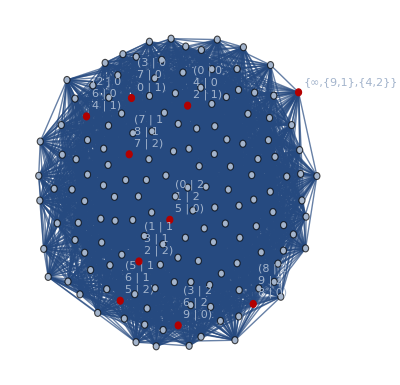
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[HighlightGraph[STSGraph[v],FindIndependentVertexSet@STSGraph[v],VertexLabels->Automatic],{v,7,31,6}]
```

```mathematica
GraphToughness[g_]:=Min[Divide@@@Select[Table[{i,Max[Length@ConnectedComponents@Subgraph[g,#]&/@Subsets[VertexList[g],{VertexCount[g]-i}]]},{i,VertexCount[g]-1}],Last[#]≥2&]]
```

```mathematica
STSGraph[9]//GraphToughness
```

3

```mathematica
STSGraph[13]//VertexCount
```

26

```mathematica
1->2//FullForm
```

Rule[1,2]

```mathematica
Thread@Rule[VertexList@STSGraph[13],Range[0,VertexCount@STSGraph[13]-1]]
```

{{{0,0},{1,0},{2,1}}→0,{{0,0},{2,0},{1,1}}→1,{{0,0},{3,0},{3,1}}→2,{{1,0},{2,0},{3,1}}→3,{{1,0},{3,0},{0,1}}→4,{{2,0},{3,0},{2,1}}→5,{{0,1},{2,1},{1,2}}→6,{{1,1},{2,1},{3,2}}→7,{{2,1},{3,1},{2,2}}→8,{{0,2},{2,2},{1,0}}→9,{{1,2},{3,2},{0,0}}→10,{∞,{2,1},{0,2}}→11,{∞,{2,2},{0,0}}→12,{∞,{3,2},{1,0}}→13,{{0,0},{0,1},{0,2}}→14,{{1,0},{1,1},{1,2}}→15,{{0,1},{1,1},{2,2}}→16,{{1,1},{3,1},{0,2}}→17,{{0,2},{1,2},{2,0}}→18,{{2,2},{3,2},{2,0}}→19,{∞,{2,0},{0,1}}→20,{∞,{3,0},{1,1}}→21,{{0,1},{3,1},{3,2}}→22,{{0,2},{3,2},{3,0}}→23,{{1,2},{2,2},{3,0}}→24,{∞,{3,1},{1,2}}→25}

```mathematica
StringJoin[ToString[#1]<>" "<>ToString[#2]<>"\n"&@@@(EdgeList@STSGraph[13]/.%4)]
```

0 1
0 2
0 3
0 4
0 5
0 6
0 7
0 8
0 9
0 10
0 11
0 12
0 13
0 14
0 15
1 2
1 3
1 5
1 16
1 7
1 17
1 18
1 10
1 19
1 20
1 12
1 21
1 14
1 15
2 3
2 4
2 5
2 22
2 17
2 8
2 23
2 24
2 10
2 12
2 21
2 25
2 14
3 4
3 5
3 22
3 17
3 8
3 18
3 9
3 19
3 20
3 25
3 13
3 15
4 5
4 16
4 6
4 22
4 9
4 23
4 24
4 20
4 21
4 13
4 14
4 15
5 6
5 7
5 8
5 18
5 23
5 24
5 19
5 20
5 11
5 21
16 6
16 22
16 7
16 17
16 8
16 9
16 24
16 19
16 20
16 12
16 21
16 14
16 15
6 22
6 7
6 8
6 18
6 24
6 10
6 20
6 11
6 25
6 14
6 15
22 7
22 17
22 8
22 23
22 10
22 19
22 20
22 25
22 13
22 14
7 17
7 8
7 23
7 10
7 19
7 11
7 21
7 13
7 15
17 8
17 18
17 9
17 23
17 11
17 21
17 25
17 14
17 15
8 9
8 24
8 19
8 11
8 12
8 25
18 9
18 23
18 24
18 10
18 19
18 20
18 11
18 25
18 14
18 15
9 23
9 24
9 19
9 11
9 12
9 13
9 14
9 15
23 24
23 10
23 19
23 11
23 21
23 13
23 14
24 10
24 19
24 12
24 21
24 25
24 15
10 19
10 12
10 25
10 13
10 14
10 15
19 20
19 12
19 13
20 11
20 12
20 21
20 25
20 13
20 14
11 12
11 21
11 25
11 13
11 14
12 21
12 25
12 13
12 14
21 25
21 13
21 15
25 13
25 15
13 15

```mathematica
g=Graph[VertexList@STSGraph[13]/.%,EdgeList@STSGraph[13]/.%];
```

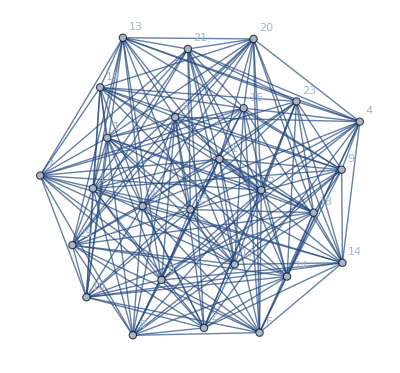

```mathematica
GraphPlot[g,VertexLabels->Automatic]
```

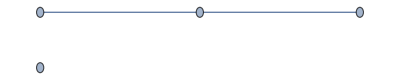

```mathematica
Subgraph[g,{2,6,8,13}]
```

```mathematica
Total[2^Complement[Range[0,25],{2,6,8,13}]]
```

67100347

```mathematica
FromDigits@IntegerDigits[%22,2]
```

11111111111101111010111011

```mathematica
IntegerDigits[23067646,2]
```

{1,0,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,0}

```mathematica
Position[Reverse[%29],0]
```

{{1},{11},{22},{24}}

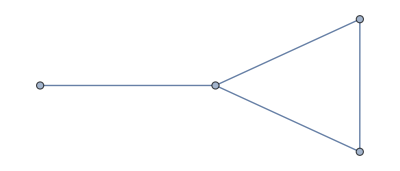

```mathematica
Subgraph[g,{2,12,23,25}]
```